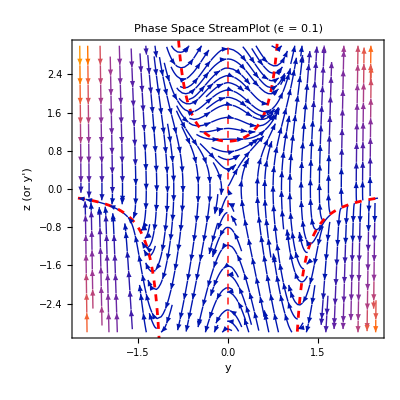

```mathematica
ClearAll[y,z,eps,dy,dz];

(*设置扰动参数*)
eps=0.1;

(*定义动力系统*)
dy=z;
dz=(y-z*y*(1-y^2))/eps;

(*绘制 StreamPlot*)
StreamPlot[{dy,dz},{y,-2.5,2.5},{z,-3,3},FrameLabel->{"y","z (or y')"},PlotLabel->Row[{"Phase Space StreamPlot (ϵ = ",eps,")"}],StreamStyle->Blue,StreamPoints->Fine,Epilog->{Red,Dashed,Thick,(*慢流形 1:y=0*)Line[{{0,-3},{0,3}}],(*慢流形 2:z=1/(1-y^2)*)Plot[1/(1-y^2),{y,-2.5,2.5},PlotStyle->{Red,Dashed,Thick},Exclusions->{y==-1,y==1}][[1]]},PlotRange->{{-2.5,2.5},{-3,3}}]
```

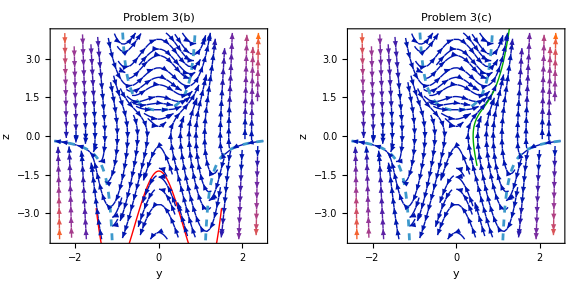

```mathematica
ClearAll[y,z,eps,sol3b,sol3c,stream];
Needs["NDSolve`FEM`"];

eps=0.1;

(*背景流线与慢流形*)
stream=StreamPlot[{z,(y-z*y*(1-y^2))/eps},{y,-2.5,2.5},{z,-4,4},StreamStyle->LightGray,Epilog->{Red,Dashed,Thick,Plot[1/(1-y^2),{y,-2.5,2.5},Exclusions->{y==-1,y==1}][[1]]}];

(*求解 3(b): \alpha=3/2, \beta=-3/2*)
sol3b=NDSolve[{eps*y''[x]+y[x]*(1-y[x]^2)*y'[x]-y[x]==0,y[0]==1.5,y[1]==-1.5},y,{x,0,1},Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}},InitialSeeding->{y[x]==1.5-3*x}];

(*求解 3(c): \alpha=1/2, \beta=2*)
sol3c=NDSolve[{eps*y''[x]+y[x]*(1-y[x]^2)*y'[x]-y[x]==0,y[0]==0.5,y[1]==2},y,{x,0,1},Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}},InitialSeeding->{y[x]==0.5+1.5*x}];

(*绘制并组合*)
GraphicsGrid[{{Show[stream,ParametricPlot[Evaluate[{y[x],y'[x]}/. sol3b],{x,0,1},PlotStyle->{Red,Thick}],FrameLabel->{"y","z"},PlotLabel->"Problem 3(b)"],Show[stream,ParametricPlot[Evaluate[{y[x],y'[x]}/. sol3c],{x,0,1},PlotStyle->{Darker[Green],Thick}],FrameLabel->{"y","z"},PlotLabel->"Problem 3(c)"]}},ImageSize->Large]
```

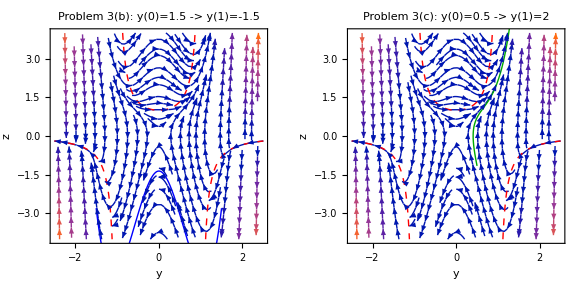

```mathematica
ClearAll[y,z,eps,sol3b,sol3c,stream,nullcline];
Needs["NDSolve`FEM`"];

eps=0.1;

(*1. 背景流线图 (浅灰色)*)
stream=StreamPlot[{z,(y-z*y*(1-y^2))/eps},{y,-2.5,2.5},{z,-4,4},StreamStyle->LightGray];

(*2. 慢流形/零倾线 (锁定为醒目的红色、粗虚线)*)
nullcline=Plot[1/(1-y^2),{y,-2.5,2.5},PlotStyle->Directive[Red,Dashed,Thick],Exclusions->{y==-1,y==1},PlotRange->{-4,4}];

(*3. 求解 3(b): \alpha=3/2, \beta=-3/2*)
sol3b=NDSolve[{eps*y''[x]+y[x]*(1-y[x]^2)*y'[x]-y[x]==0,y[0]==1.5,y[1]==-1.5},y,{x,0,1},Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}},InitialSeeding->{y[x]==1.5-3*x}];

(*4. 求解 3(c): \alpha=1/2, \beta=2*)
sol3c=NDSolve[{eps*y''[x]+y[x]*(1-y[x]^2)*y'[x]-y[x]==0,y[0]==0.5,y[1]==2},y,{x,0,1},Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}},InitialSeeding->{y[x]==0.5+1.5*x}];

(*5. 组合绘制：使用 Show 保证图层层叠不会互相干扰颜色*)
GraphicsGrid[{{Show[stream,nullcline,ParametricPlot[Evaluate[{y[x],y'[x]}/. sol3b],{x,0,1},PlotStyle->Directive[Blue,Thick]],FrameLabel->{"y","z"},PlotLabel->"Problem 3(b): y(0)=1.5 -> y(1)=-1.5"],Show[stream,nullcline,ParametricPlot[Evaluate[{y[x],y'[x]}/. sol3c],{x,0,1},PlotStyle->Directive[Darker[Green],Thick]],FrameLabel->{"y","z"},PlotLabel->"Problem 3(c): y(0)=0.5 -> y(1)=2"]}},ImageSize->Large]
```